```mathematica
(* The graphical representation of the problem *)
```

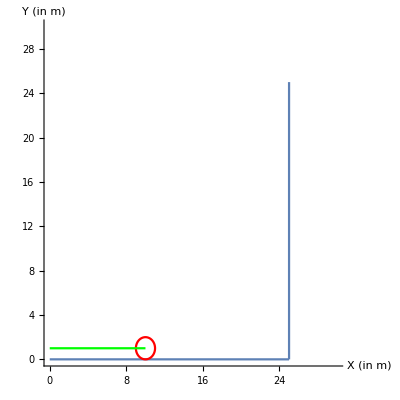

```mathematica
Show[
Plot[0,{x,0,25}],
ParametricPlot[{25,x},{x,0,25}],
ParametricPlot[{10+Cos[θ],1+Sin[θ]},{θ,0,2π},PlotStyle->Red],
ParametricPlot[{x,1},{x,0,10},PlotStyle->Green],
AxesOrigin->{0,-1},PlotRange->{{0,30},{0,30}},AspectRatio->1,AxesLabel->{"X (in m)","Y (in m)"}
]
```

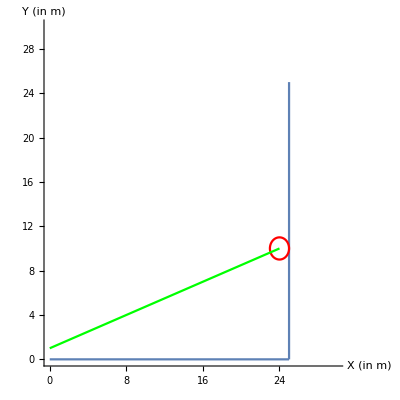

```mathematica
Show[
Plot[0,{x,0,25}],
ParametricPlot[{25,x},{x,0,25}],
ParametricPlot[{24+Cos[θ],10+Sin[θ]},{θ,0,2π},PlotStyle->Red],
Plot[9/24x+1,{x,0,24},PlotStyle->Green],
AxesOrigin->{0,-1},PlotRange->{{0,30},{0,30}},AspectRatio->1,AxesLabel->{"X (in m)","Y (in m)"}
]
```

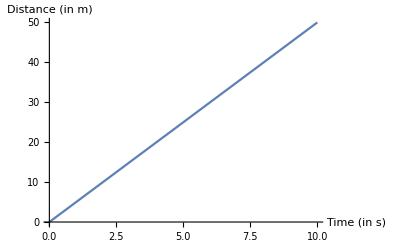

```mathematica
Plot[5x,{x,0,10},AxesLabel->{"Time (in s)","Distance (in m)"},PlotLegends->"Distance vs time curve"]
```

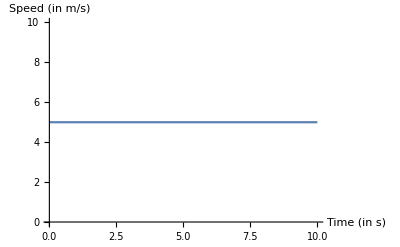

```mathematica
Plot[5,{x,0,10},AxesLabel->{"Time (in s)","Speed (in m/s)"},PlotLegends->"Speed vs time curve"]
```

```mathematica
Expand[625+25(x-5)^2]
```

1250-250 x+25 x^2

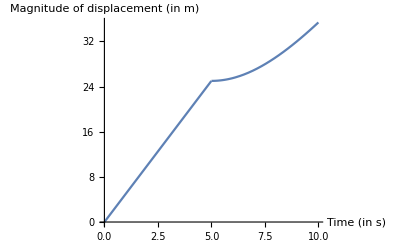

```mathematica
Plot[If[5<x<10,Sqrt[1250-250 x+25 x^2],5x],{x,0,10},AxesLabel->{"Time (in s)","Magnitude of displacement (in m)"},PlotLegends->"Magnitude of displacement vs time curve"]
```

```mathematica
D[Sqrt[1250-250 x+25 x^2],x]//FullSimplify
```

(5 (-5+x))/(√(50+(-10+x) x))

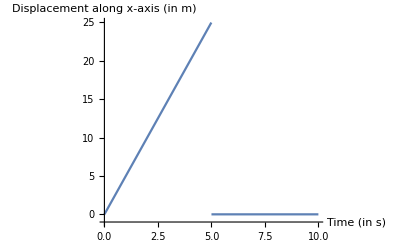

```mathematica
Plot[If[5<x<10,0,5x],{x,0,10},AxesLabel->{"Time (in s)","Displacement along x-axis (in m)"},PlotLegends->"Displacement along x-axis vs time curve",AxesOrigin->{0,-1},PlotRange->{{0,10},{-1,25}}]
```

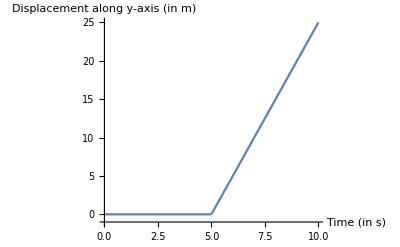

```mathematica
Plot[If[5<x<10,5(x-5),0],{x,0,10},AxesLabel->{"Time (in s)","Displacement along y-axis (in m)"},PlotLegends->"Displacement along y-axis vs time curve",AxesOrigin->{0,-1}]
```

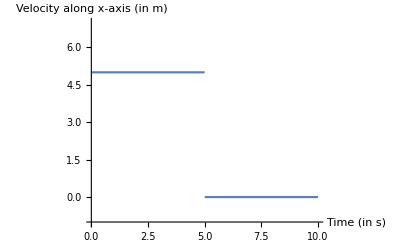

```mathematica
Plot[If[5<x<10,0,5],{x,0,10},AxesLabel->{"Time (in s)","Velocity along x-axis (in m)"},PlotLegends->"Velocity along x-axis vs time curve",AxesOrigin->{0,-1},PlotRange->{{0,10},{-1,7}}]
```

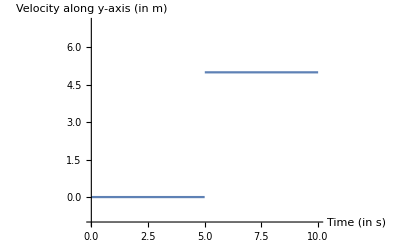

```mathematica
Plot[If[5<x<10,5,0],{x,0,10},AxesLabel->{"Time (in s)","Velocity along y-axis (in m)"},PlotLegends->"Velocity along y-axis vs time curve",AxesOrigin->{0,-1},PlotRange->{{0,10},{-1,7}}]
```

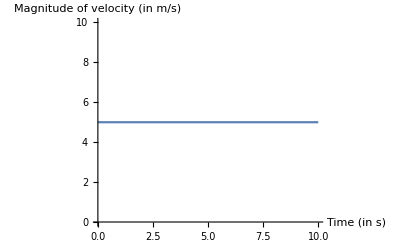

```mathematica
Plot[5,{x,0,10},AxesLabel->{"Time (in s)","Magnitude of velocity (in m/s)"},PlotLegends->"Magnitude of velocity vs time curve"]
```

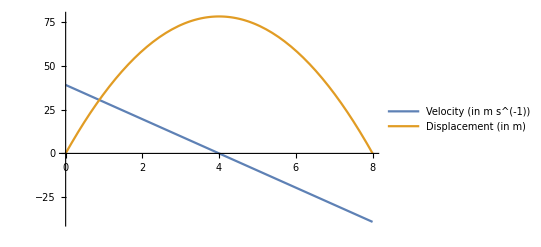

```mathematica
Block[{u=39.2,g=9.8},Plot[{u-g t,u t-1/2 g t^2},{t,0,8},PlotLegends->{"Velocity (in m s^(-1))","Displacement (in m)"}]]
```

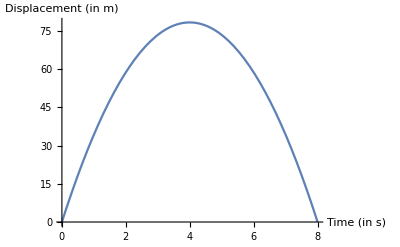

```mathematica
Block[{u=39.2,g=9.8},Plot[u t-1/2 g t^2,{t,0,8},AxesLabel->{"Time (in s)","Displacement (in m)"}]]
```

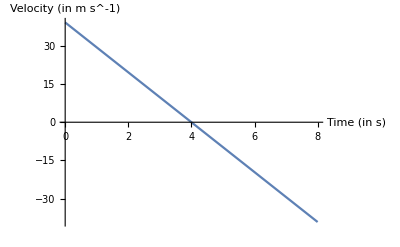

```mathematica
Block[{u=39.2,g=9.8},Plot[u-g t,{t,0,8},AxesLabel->{"Time (in s)","Velocity (in m s^-1)"}]]
```

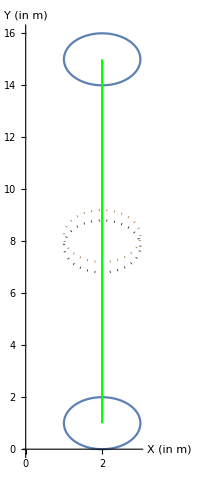

```mathematica
Show[
ParametricPlot[{2+Cos[θ],1+Sin[θ]},{θ,0,2π}],
ParametricPlot[{2+Cos[θ],7.8+Sin[θ]},{θ,0,2π},PlotStyle->{Black,Dotted}],
ParametricPlot[{2+Cos[θ],8.2+Sin[θ]},{θ,0,2π},PlotStyle->{Brown,Dotted}],
ParametricPlot[{2+Cos[θ],15+Sin[θ]},{θ,0,2π}],
ParametricPlot[{2,x},{x,1,15},PlotStyle->Green],
AxesOrigin->{0,0},PlotRange->{{0,3},{0,16}},AxesLabel->{"X (in m)","Y (in m)"}
]
```

```mathematica
D[3 Sin[2 π t],t]
```

6 π Cos[2 π t]

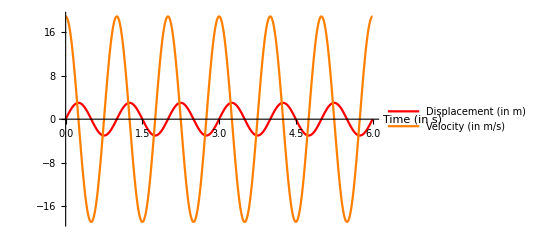

```mathematica
Plot[{3 Sin[2 π t],6 π Cos[2 π t]},{t,0,6},PlotStyle->{Red,Orange},PlotLegends->{"Displacement (in m)", "Velocity (in m/s)"},AxesLabel->{"Time (in s)"}]
```

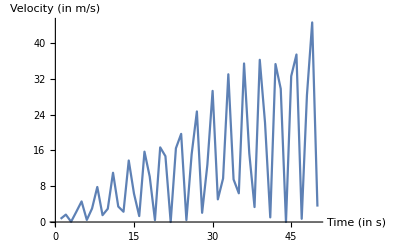

```mathematica
ListLinePlot[Table[k*Sin[k]^2,{k,1,50}],AxesLabel->{"Time (in s)","Velocity (in m/s)"}]
```

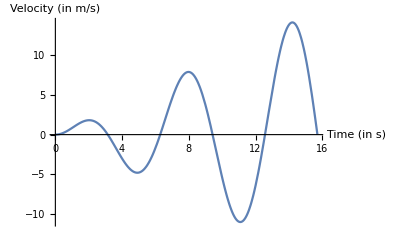

```mathematica
Plot[x Sin[x],{x,0,5π},AxesLabel->{"Time (in s)","Velocity (in m/s)"}]
```

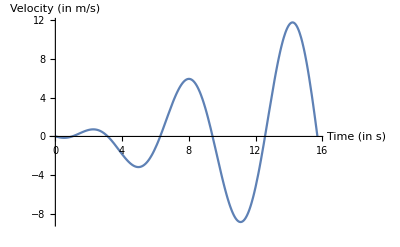

```mathematica
Plot[(x-x^(1/3)) Sin[x],{x,0,5π},AxesLabel->{"Time (in s)","Velocity (in m/s)"}]
```

```mathematica
(* Analysing circular motion *)
```

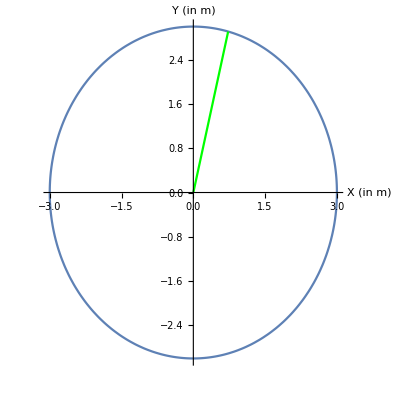

```mathematica
Show[
ParametricPlot[{3 Cos[2π t],3 Sin[2π t]},{t,0,1}],
Plot[4x,{x,0,3 Cos[ArcTan[4]]},PlotStyle->Green],
AxesLabel->{"X (in m)","Y (in m)"}
]
```

```mathematica
Manipulate[
Show[
ParametricPlot[{r0 Cos[ω t],r0 Sin[ω t]},{t,0,2π}],
Plot[x Tan[ω tf],{x,0,r0 Cos[ω tf]},PlotStyle->Green],
Plot[r0 Sin[ω(t-1.5r0)],{t,1.5r0,1.5r0+tf},PlotStyle->Red],
AxesLabel->{"X (in m)","Y (in m)"},PlotRange->{{-r0,1.5r0+6π},{-1.5r0,1.5 r0}},AspectRatio->Automatic
],{tf,0.01,6π},{r0,1,4},{ω,1,4}
]
```

```mathematica
Clear[r0,ω]
```

```mathematica
Manipulate[
Show[
ParametricPlot[{3.495Cos[1.635 t],3.495Sin[1.635t]},{t,0,2π}],
Plot[x Tan[1.635 tf],{x,0,3.495 Cos[1.635 tf]},PlotStyle->Green],
Plot[3.495 Sin[1.635(t-1.5*3.495)],{t,1.5*3.495,1.5*3.495+tf},PlotStyle->Red],
AxesLabel->{"X (in m)","Y (in m)"},PlotRange->{{-3.495,1.5*3.495+6π},{-1.5*3.495,1.5*3.495}},AspectRatio->Automatic
],{tf,0.01,6π}
]
```

```mathematica
Directory[]
```

/Users/shrohanmohapatra

```mathematica
SetDirectory["//Users//shrohanmohapatra//Documents//PersonalFolder"]
```

/Users/shrohanmohapatra/Documents/PersonalFolder

```mathematica
Directory[]
```

/Users/shrohanmohapatra/Documents/PersonalFolder

```mathematica
Export["physicsGif1.gif",Manipulate[
Show[
ParametricPlot[{3.495Cos[1.635 t],3.495Sin[1.635t]},{t,0,2π}],
Plot[x Tan[1.635 tf],{x,0,3.495 Cos[1.635 tf]},PlotStyle->Green],
Plot[3.495 Sin[1.635(t-1.5*3.495)],{t,1.5*3.495,1.5*3.495+tf},PlotStyle->Red],
AxesLabel->{"X (in m)","Y (in m)"},PlotRange->{{-3.495,1.5*3.495+6π},{-1.5*3.495,1.5*3.495}},AspectRatio->Automatic
],{tf,0.01,6π}
]]
```

physicsGif1.gif

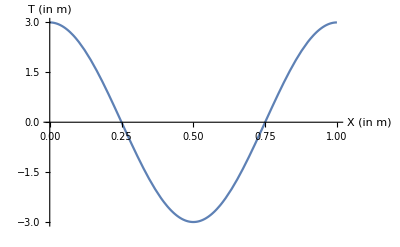

```mathematica
Plot[3 Cos[2π t],{t,0,1},AxesLabel->{"X (in m)","T (in m)"}]
```

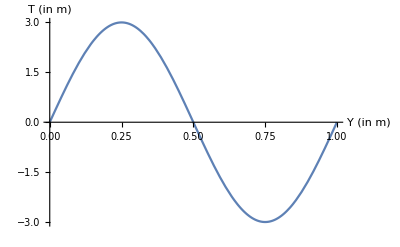

```mathematica
Plot[3 Sin[2π t],{t,0,1},AxesLabel->{"Y (in m)","T (in m)"}]
```

```mathematica
D[r[t]Cos[θ[t]],{t,2}]//FullSimplify
```

Cos[θ[t]] (-r[t] θ'[t]^2+r''[t])-Sin[θ[t]] (2 r'[t] θ'[t]+r[t] θ''[t])

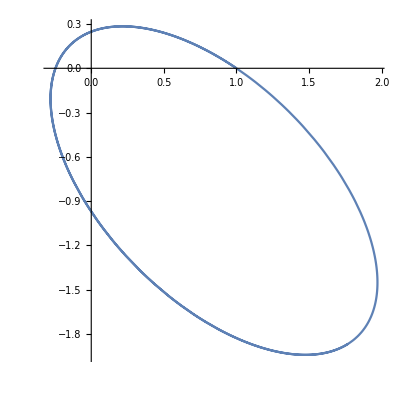

```mathematica
Block[
{r=1,ux=-15,uy=10,m=9.1*10^(-31),q=1.6*10^(-19),ϵ0=8.85*10^(-12),x,y,t,soln},
soln=NDSolve[
{
D[x[t],{t,2}]==-q^2 x[t]/(4 π ϵ0 m (x[t]^2+y[t]^2)^(3/2)),
D[y[t],{t,2}]==-q^2 y[t]/(4 π ϵ0 m (x[t]^2+y[t]^2)^(3/2)),
x[0]==r,y[0]==0,x'[0]==ux,y'[0]==uy
},{x[t],y[t]},{t,0,1}
];
ParametricPlot[{x[t],y[t]}/.soln[[1]],{t,0,1}]
]
```

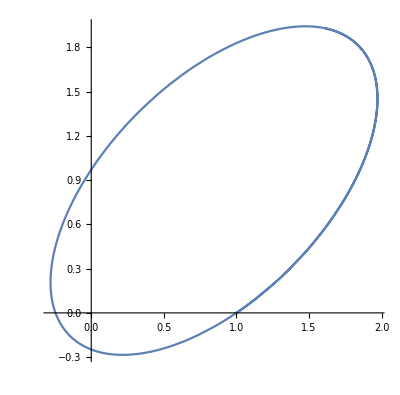

```mathematica
Block[
{r=1,ux=15,uy=10,m=9.1*10^(-31),q=1.6*10^(-19),ϵ0=8.85*10^(-12),x,y,t,soln},
soln=NDSolve[
{
D[x[t],{t,2}]==-q^2 x[t]/(4 π ϵ0 m (x[t]^2+y[t]^2)^(3/2)),
D[y[t],{t,2}]==-q^2 y[t]/(4 π ϵ0 m (x[t]^2+y[t]^2)^(3/2)),
x[0]==r,y[0]==0,x'[0]==ux,y'[0]==uy
},{x[t],y[t]},{t,0,1}
];
ParametricPlot[{x[t],y[t]}/.soln[[1]],{t,0,1}]
]
```

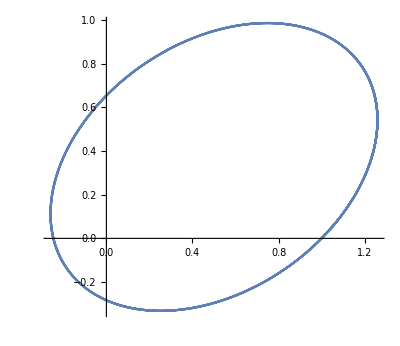

```mathematica
Block[
{r=1,ux=10,uy=10,m=9.1*10^(-31),q=1.6*10^(-19),ϵ0=8.85*10^(-12),x,y,t,soln},
soln=NDSolve[
{
D[x[t],{t,2}]==-q^2 x[t]/(4 π ϵ0 m (x[t]^2+y[t]^2)^(3/2)),
D[y[t],{t,2}]==-q^2 y[t]/(4 π ϵ0 m (x[t]^2+y[t]^2)^(3/2)),
x[0]==r,y[0]==0,x'[0]==ux,y'[0]==uy
},{x[t],y[t]},{t,0,1}
];
ParametricPlot[{x[t],y[t]}/.soln[[1]],{t,0,1}]
]
```

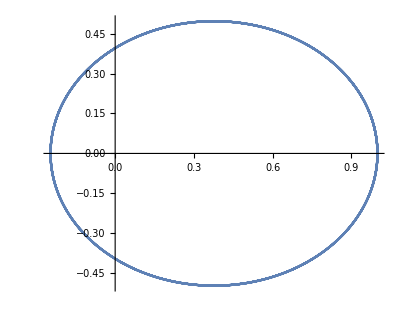

```mathematica
Block[
{r=1,ux=0,uy=10,m=9.1*10^(-31),q=1.6*10^(-19),ϵ0=8.85*10^(-12),x,y,t,soln},
soln=NDSolve[
{
D[x[t],{t,2}]==-q^2 x[t]/(4 π ϵ0 m (x[t]^2+y[t]^2)^(3/2)),
D[y[t],{t,2}]==-q^2 y[t]/(4 π ϵ0 m (x[t]^2+y[t]^2)^(3/2)),
x[0]==r,y[0]==0,x'[0]==ux,y'[0]==uy
},{x[t],y[t]},{t,0,1}
];
ParametricPlot[{x[t],y[t]}/.soln[[1]],{t,0,1}]
]
```

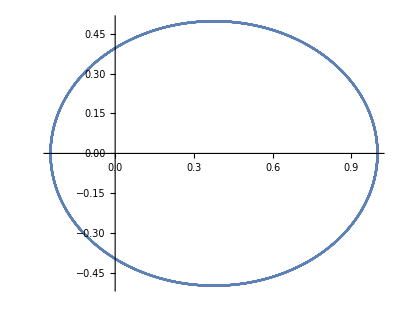

```mathematica
Block[
{r=1,ux=0,uy=-10,m=9.1*10^(-31),q=1.6*10^(-19),ϵ0=8.85*10^(-12),x,y,t,soln},
soln=NDSolve[
{
D[x[t],{t,2}]==-q^2 x[t]/(4 π ϵ0 m (x[t]^2+y[t]^2)^(3/2)),
D[y[t],{t,2}]==-q^2 y[t]/(4 π ϵ0 m (x[t]^2+y[t]^2)^(3/2)),
x[0]==r,y[0]==0,x'[0]==ux,y'[0]==uy
},{x[t],y[t]},{t,0,1}
];
ParametricPlot[{x[t],y[t]}/.soln[[1]],{t,0,1}]
]
```

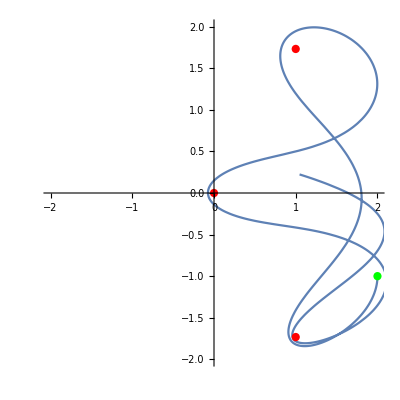

```mathematica
Block[
{a=1,ux=0,uy=-10,m=9.1*10^(-31),q=1.6*10^(-19),ϵ0=8.85*10^(-12),x,y,t,soln,sx,sy},
sx=2a;
sy=-a;
soln=NDSolve[
{
D[x[t],{t,2}]==-q^2 /(4 π ϵ0 m) (x[t]/(x[t]^2+y[t]^2)^(3/2)+(x[t]-a)/((x[t]-a)^2+(y[t]-Sqrt[3]a)^2)^(3/2)+(x[t]-a)/((x[t]-a)^2+(y[t]+Sqrt[3]a)^2)^(3/2)),
D[y[t],{t,2}]==-q^2 /(4 π ϵ0 m)(y[t]/(x[t]^2+y[t]^2)^(3/2)+(y[t]-Sqrt[3]a)/((x[t]-a)^2+(y[t]-Sqrt[3]a)^2)^(3/2)+(y[t]+Sqrt[3]a)/((x[t]-a)^2+(y[t]+Sqrt[3]a)^2)^(3/2)),
x[0]==sx,y[0]==sy,x'[0]==ux,y'[0]==uy
},{x[t],y[t]},{t,0,1}
];
Show[
ParametricPlot[{x[t],y[t]}/.soln[[1]],{t,0,1}],
Graphics[{Red,Disk[{0,0},0.05a]}],Graphics[{Red,Disk[{a,Sqrt[3]a},0.05a]}],Graphics[{Red,Disk[{a,-Sqrt[3]a},0.05a]}],
Graphics[{Green,Disk[{sx,sy},0.05a]}],
PlotRange->{{-2a,2a},{-2a,2a}}
]
]
```

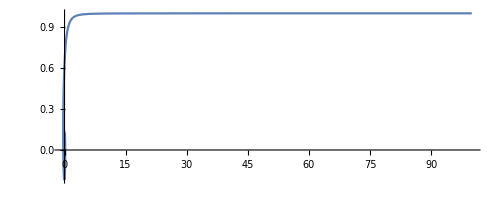

```mathematica
PolarPlot[1/θ,{θ,0.01,10π}]
```

```mathematica
D[r0 Cos[ω t]/ω/t,{t,2}]//Together
```

-(r0 (-2 Cos[t ω]+t^2 ω^2 Cos[t ω]-2 t ω Sin[t ω]))/(t^3 ω)

```mathematica
D[r0 Sin[ω t]/ω/t,{t,2}]//Together
```

-(r0 (2 t ω Cos[t ω]-2 Sin[t ω]+t^2 ω^2 Sin[t ω]))/(t^3 ω)

```mathematica
(-(r0 (-2 ω t x/r0 ω t+t^2 ω^2 y/r0 ω t-2 t ω y/r0 ω t))/(t^3 ω))//FullSimplify
```

(ω (2 (x+y)-t y ω))/t

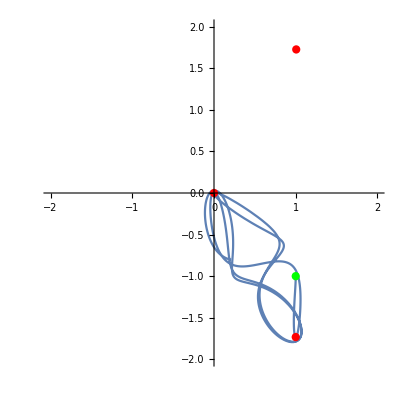

```mathematica
Block[
{a=1,ux=0,uy=-10,m=9.1*10^(-31),q=1.6*10^(-19),ϵ0=8.85*10^(-12),x,y,t,soln,sx,sy},
sx=a;
sy=-a;
soln=NDSolve[
{
D[x[t],{t,2}]==-q^2 /(4 π ϵ0 m) (x[t]/(x[t]^2+y[t]^2)^(3/2)+(x[t]-a)/((x[t]-a)^2+(y[t]-Sqrt[3]a)^2)^(3/2)+(x[t]-a)/((x[t]-a)^2+(y[t]+Sqrt[3]a)^2)^(3/2)),
D[y[t],{t,2}]==-q^2 /(4 π ϵ0 m)(y[t]/(x[t]^2+y[t]^2)^(3/2)+(y[t]-Sqrt[3]a)/((x[t]-a)^2+(y[t]-Sqrt[3]a)^2)^(3/2)+(y[t]+Sqrt[3]a)/((x[t]-a)^2+(y[t]+Sqrt[3]a)^2)^(3/2)),
x[0]==sx,y[0]==sy,x'[0]==ux,y'[0]==uy
},{x[t],y[t]},{t,0,1}
];
Show[
ParametricPlot[{x[t],y[t]}/.soln[[1]],{t,0,1}],
Graphics[{Red,Disk[{0,0},0.05a]}],Graphics[{Red,Disk[{a,Sqrt[3]a},0.05a]}],Graphics[{Red,Disk[{a,-Sqrt[3]a},0.05a]}],
Graphics[{Green,Disk[{sx,sy},0.05a]}],
PlotRange->{{-2a,2a},{-2a,2a}}
]
]
```

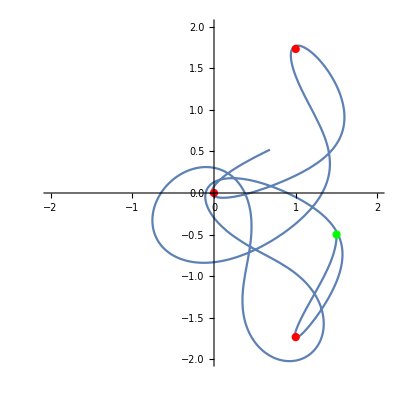

```mathematica
Block[
{a=1,ux=0,uy=-10,m=9.1*10^(-31),q=1.6*10^(-19),ϵ0=8.85*10^(-12),x,y,t,soln,sx,sy},
sx=1.5a;
sy=-0.5a;
soln=NDSolve[
{
D[x[t],{t,2}]==-q^2 /(4 π ϵ0 m) (x[t]/(x[t]^2+y[t]^2)^(3/2)+(x[t]-a)/((x[t]-a)^2+(y[t]-Sqrt[3]a)^2)^(3/2)+(x[t]-a)/((x[t]-a)^2+(y[t]+Sqrt[3]a)^2)^(3/2)),
D[y[t],{t,2}]==-q^2 /(4 π ϵ0 m)(y[t]/(x[t]^2+y[t]^2)^(3/2)+(y[t]-Sqrt[3]a)/((x[t]-a)^2+(y[t]-Sqrt[3]a)^2)^(3/2)+(y[t]+Sqrt[3]a)/((x[t]-a)^2+(y[t]+Sqrt[3]a)^2)^(3/2)),
x[0]==sx,y[0]==sy,x'[0]==ux,y'[0]==uy
},{x[t],y[t]},{t,0,1}
];
Show[
ParametricPlot[{x[t],y[t]}/.soln[[1]],{t,0,1}],
Graphics[{Red,Disk[{0,0},0.05a]}],Graphics[{Red,Disk[{a,Sqrt[3]a},0.05a]}],Graphics[{Red,Disk[{a,-Sqrt[3]a},0.05a]}],
Graphics[{Green,Disk[{sx,sy},0.05a]}],
PlotRange->{{-2a,2a},{-2a,2a}}
]
]
```

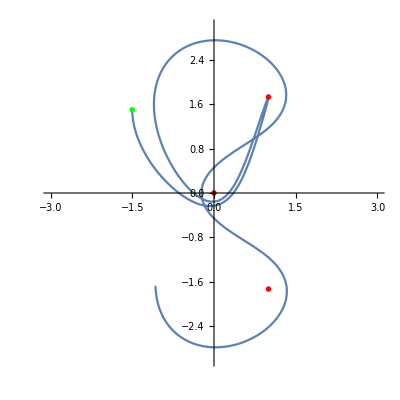

```mathematica
Block[
{a=1,ux=0,uy=-10,m=9.1*10^(-31),q=1.6*10^(-19),ϵ0=8.85*10^(-12),x,y,t,soln,sx,sy},
sx=-1.5a;
sy=1.5a;
soln=NDSolve[
{
D[x[t],{t,2}]==-q^2 /(4 π ϵ0 m) (x[t]/(x[t]^2+y[t]^2)^(3/2)+(x[t]-a)/((x[t]-a)^2+(y[t]-Sqrt[3]a)^2)^(3/2)+(x[t]-a)/((x[t]-a)^2+(y[t]+Sqrt[3]a)^2)^(3/2)),
D[y[t],{t,2}]==-q^2 /(4 π ϵ0 m)(y[t]/(x[t]^2+y[t]^2)^(3/2)+(y[t]-Sqrt[3]a)/((x[t]-a)^2+(y[t]-Sqrt[3]a)^2)^(3/2)+(y[t]+Sqrt[3]a)/((x[t]-a)^2+(y[t]+Sqrt[3]a)^2)^(3/2)),
x[0]==sx,y[0]==sy,x'[0]==ux,y'[0]==uy
},{x[t],y[t]},{t,0,1}
];
Show[
ParametricPlot[{x[t],y[t]}/.soln[[1]],{t,0,1}],
Graphics[{Red,Disk[{0,0},0.05a]}],Graphics[{Red,Disk[{a,Sqrt[3]a},0.05a]}],Graphics[{Red,Disk[{a,-Sqrt[3]a},0.05a]}],
Graphics[{Green,Disk[{sx,sy},0.05a]}],
PlotRange->{{-3a,3a},{-3a,3a}}
]
]
```

```mathematica
Integrate[1/Sqrt[μ^2+λ/m/r+L^2/2/m^2/r^2],r]//Together
```

(√2 L^2 μ+2 √2 m r λ μ+2 √2 m^2 r^2 μ^3-λ √(L^2+2 m r λ+2 m^2 r^2 μ^2) Log[λ+μ (2 m r μ+√2 √(L^2+2 m r (λ+m r μ^2)))])/(2 m^2 r μ^3 √((L^2+2 m r λ+2 m^2 r^2 μ^2)/(m^2 r^2)))

```mathematica
FullSimplify[(√2 L^2 μ+2 √2 m r λ μ+2 √2 m^2 r^2 μ^3)/(2 m^2 r μ^3 √((L^2+2 m r λ+2 m^2 r^2 μ^2)/(m^2 r^2)))]
```

(r √((L^2+2 m r λ)/(2 m^2 r^2)+μ^2))/μ^2

```mathematica
FullSimplify[-λ √(L^2+2 m r λ+2 m^2 r^2 μ^2)/(2 m^2 r μ^3 √((L^2+2 m r λ+2 m^2 r^2 μ^2)/(m^2 r^2))),Assumptions->{m>0&&r>0&&μ>0&&λ∈Reals&&L∈Reals}]
```

-λ/(2 m μ^3)

```mathematica
Expand[2(L^2+2 m r (λ+m r μ^2))]
```

2 L^2+4 m r λ+4 m^2 r^2 μ^2

```mathematica
Integrate[(L/μ/m)/r^2 1/Sqrt[1+λ/(m μ^2 r)+L^2/(2 m^2 μ^2 r^2)],r]
```

(√2 √(L^2+2 m r (λ+m r μ^2)) (Log[r]-Log[L^2+m r λ+L √(L^2+2 m r (λ+m r μ^2))]))/(m r μ √((L^2+2 m r (λ+m r μ^2))/(m^2 r^2 μ^2)))

```mathematica
FullSimplify[(√2 √(L^2+2 m r (λ+m r μ^2)) (Log[r]-Log[L^2+m r λ+L √(L^2+2 m r (λ+m r μ^2))]))/(m r μ √((L^2+2 m r (λ+m r μ^2))/(m^2 r^2 μ^2))),Assumptions->{m>0&&r>0&&μ>0&&λ∈Reals&&L∈Reals}]
```

√2 (Log[r]-Log[m r λ+L (L+√(L^2+2 m r (λ+m r μ^2)))])

```mathematica
FullSimplify[(m r λ+L (L+√(L^2+2 m r (λ+m r μ^2))))/r]
```

m λ+(L (L+√(L^2+2 m r (λ+m r μ^2))))/r

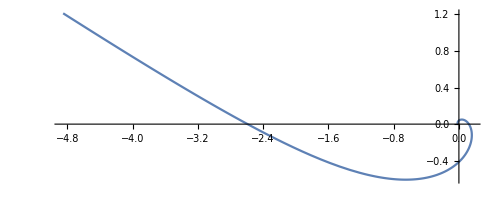

```mathematica
Block[
{r,θ,m=1,L=2,μ=3/2,λ=4/5},
ParametricPlot[{r Cos[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]],r Sin[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]]},{r,0.01,5}]
]
```

```mathematica
Block[
{r,θ,m=1,L=2,μ=-3/2,λ=4/5},
ParametricPlot[{r Cos[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]],r Sin[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]]},{r,0.01,5}]
]
```

-Graphics-

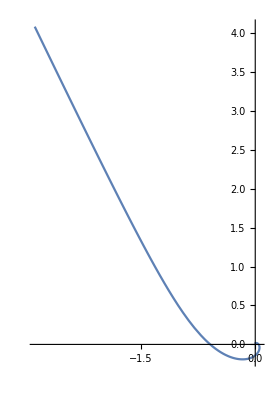

```mathematica
Block[
{r,θ,m=1,L=1.2,μ=3/2,λ=4/5},
ParametricPlot[{r Cos[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]],r Sin[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]]},{r,0.01,5}]
]
```

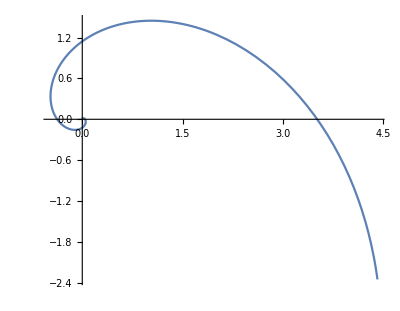

```mathematica
Block[
{r,θ,m=1,L=100,μ=3/2,λ=4/5},
ParametricPlot[{r Cos[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]],r Sin[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]]},{r,0.01,5}]
]
```

```mathematica
Block[
{r,θ,m=1,L=2,μ=3/2,λ=-4/5},
Table[{r Cos[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]]//Abs,r Sin[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]]//Abs},{r,0.01,10,0.5}]
]
```

{{0.425144,0.425053},{21.6791,21.681},{42.9408,42.9291},{64.1971,64.1827},{85.451,85.4386},{106.704,106.695},{127.957,127.952},{149.21,149.209},{170.464,170.465},{191.717,191.722},{212.97,212.979},{234.223,234.236},{255.476,255.492},{276.729,276.749},{297.983,298.005},{319.236,319.262},{340.489,340.519},{361.742,361.775},{382.996,383.032},{404.249,404.289}}

```mathematica
Block[
{r,θ,m=1,L=2,μ=Sqrt[2/5],λ=-4/5},
Table[{r Cos[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]],r Sin[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L+2μ^2 m^2 r^2/L^2])]]},{r,0.01,10,0.5}]
]
```

{{-0.400817+0.141752 ⅈ,-0.141791-0.400706 ⅈ},{-14.5114+16.1068 ⅈ,-16.1112-14.5074 ⅈ},{-39.9345-15.7804 ⅈ,15.7848-39.9234 ⅈ},{-23.5513-59.7063 ⅈ,59.7228-23.5448 ⅈ},{18.6033-83.3841 ⅈ,83.4071+18.5982 ⅈ},{59.917-88.2815 ⅈ,88.3059+59.9004 ⅈ},{92.3629-88.5533 ⅈ,88.5778+92.3373 ⅈ},{119.218-89.7343 ⅈ,89.7591+119.185 ⅈ},{143.328-92.2966 ⅈ,92.3222+143.288 ⅈ},{166.042-95.8721 ⅈ,95.8986+165.996 ⅈ},{187.986-100.132 ⅈ,100.16+187.934 ⅈ},{209.469-104.858 ⅈ,104.887+209.411 ⅈ},{230.658-109.911 ⅈ,109.941+230.594 ⅈ},{251.65-115.199 ⅈ,115.231+251.58 ⅈ},{272.502-120.662 ⅈ,120.696+272.427 ⅈ},{293.254-126.258 ⅈ,126.293+293.173 ⅈ},{313.931-131.957 ⅈ,131.994+313.844 ⅈ},{334.55-137.738 ⅈ,137.776+334.457 ⅈ},{355.123-143.583 ⅈ,143.623+355.025 ⅈ},{375.661-149.483 ⅈ,149.524+375.557 ⅈ}}

```mathematica
Reduce[(1-2m λ r/l^2+2m^2 μ^2 r^2/l^2)≥0&&1≥l^2/(m λ r)(1+Sqrt[1-2m λ r/l^2+2m^2 μ^2 r^2/l^2])&&λ>0&&m>0&&l>0&&μ≥0,{λ,m,l,μ,r}]
```

λ>0&&m>0&&l>0&&((μ==0&&r<0)||(0<μ<(√(λ^2/l^2))/(√2)&&(r<0||r≥λ/(2 m μ^2)+1/2 √((λ^2-2 l^2 μ^2)/(m^2 μ^4))))||(μ==(√(λ^2/l^2))/(√2)&&(r<0||r≥λ/(2 m μ^2)-1/2 √((λ^2-2 l^2 μ^2)/(m^2 μ^4))))||(μ>(√(λ^2/l^2))/(√2)&&r<0))

```mathematica
Reduce[(1-2m λ r/l^2+2m^2 μ^2 r^2/l^2)≥0&&1≥l^2/(m λ r)(1+Sqrt[1-2m λ r/l^2+2m^2 μ^2 r^2/l^2])&&λ<0&&m>0&&l>0&&μ≥0,{λ,m,l,μ,r}]
```

λ<0&&m>0&&l>0&&((μ==0&&r>0)||(0<μ≤(√(λ^2/l^2))/(√2)&&(r≤λ/(2 m μ^2)-1/2 √((λ^2-2 l^2 μ^2)/(m^2 μ^4))||r>0))||(μ>(√(λ^2/l^2))/(√2)&&r>0))

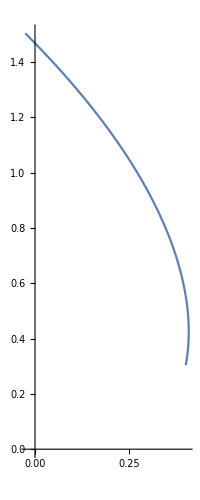

```mathematica
Block[
{r,θ,m=1,L=2,λ=-4,μ},
μ=Sqrt[λ^2/2/L^2]0.1;
ParametricPlot[{r Cos[-Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L^2+2μ^2 m^2 r^2/L^2])]],r Sin[-Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L^2+2μ^2 m^2 r^2/L^2])]]},{r,(λ/(2 m μ^2)+1/2 √((λ^2-2 L^2 μ^2)/(m^2 μ^4))),3(λ/(2 m μ^2)+1/2 √((λ^2-2 L^2 μ^2)/(m^2 μ^4)))},AxesOrigin->{0,0}]
]
```

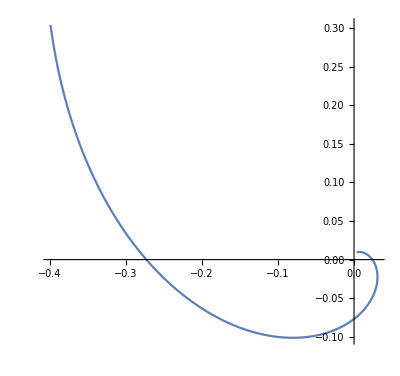

```mathematica
Block[
{r,θ,m=1,L=2,λ=4,μ},
μ=Sqrt[λ^2/2/L^2]0.1;
ParametricPlot[{r Cos[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L^2+2μ^2 m^2 r^2/L^2])]],r Sin[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L^2+2μ^2 m^2 r^2/L^2])]]},{r,0.01,(λ/(2 m μ^2)-1/2 √((λ^2-2 L^2 μ^2)/(m^2 μ^4)))},AxesOrigin->{0,0}]
]
```

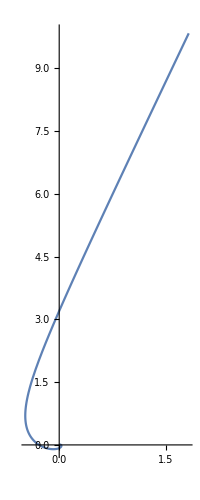

```mathematica
Block[
{r,θ,m=1,L=2,λ=4,μ},
μ=Sqrt[λ^2/2/L^2]1.5;
ParametricPlot[{r Cos[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L^2+2μ^2 m^2 r^2/L^2])]],r Sin[Sqrt[2]Log[1+L^2/(λ m r)(1+Sqrt[1+2 m λ r/L^2+2μ^2 m^2 r^2/L^2])]]},{r,0.01,10},AxesOrigin->{0,0}]
]
```